```mathematica
fin="CDA_decimation_FMS_all_K_3.txt";
stepsdec=1;
```

```mathematica
SetDirectory[NotebookDirectory[]];
lines=Select[Map[ToExpression,Map[StringSplit,ReadList[fin,String][[2;;]]]],#[[3]]==stepsdec&];
```

```mathematica
nlist=DeleteDuplicates[lines[[;;,1]]]
```

{512,1024,2048,4096,8192,16384,32768}

```mathematica
data=Table[Select[lines,#[[1]]==n&][[;;,{2,6}]],{n,nlist}];
```

```mathematica
sigmoid[x_,a_,b_]:=1.0/(1+ⅇ^(a x+b))
```

```mathematica
fits=Table[Normal[NonlinearModelFit[vals,sigmoid[x,a,b],{a,b},x]],{vals,data}]
```

{1./(1+ⅇ^(-31.8959+8.68475 x)),1./(1+ⅇ^(-48.3234+12.8966 x)),1./(1+ⅇ^(-58.3155+15.3884 x)),1./(1+ⅇ^(-88.2057+22.94 x)),1./(1+ⅇ^(-126.947+32.5307 x)),1./(1+ⅇ^(-262.578+66.6192 x)),1./(1+ⅇ^(-334.279+60.6303 x))}

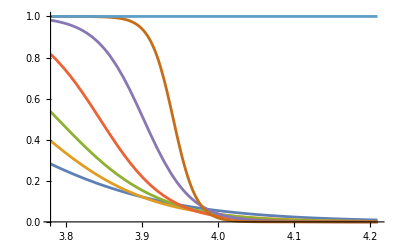

```mathematica
Plot[fits,{x,3.78,4.21}]
```

```mathematica
savedatafit[fit_,n_,stepsdec_, minalpha_,maxalpha_,dalpha_]:=Export[StringJoin["sigmoid_data_N_",ToString[n],"_stepsdec_",ToString[stepsdec],".txt"],Table[{alpha,fit/.{x->1alpha}},{alpha,minalpha,maxalpha,dalpha}],"Table","FieldSeparators"->" "]
```

```mathematica
minalpha=3.74;
maxalpha=4.3;
dalpha=0.001;
```

```mathematica
Map[savedatafit[#[[1]],#[[2]],stepsdec,minalpha,maxalpha,dalpha]&,Transpose[{fits,nlist}]]
```

{sigmoid_data_N_512_stepsdec_1.txt,sigmoid_data_N_1024_stepsdec_1.txt,sigmoid_data_N_2048_stepsdec_1.txt,sigmoid_data_N_4096_stepsdec_1.txt,sigmoid_data_N_8192_stepsdec_1.txt,sigmoid_data_N_16384_stepsdec_1.txt,sigmoid_data_N_32768_stepsdec_1.txt}

```mathematica
Table[{i,i},{i,1,10}] //N
```

{{1.,1.},{2.,2.},{3.,3.},{4.,4.},{5.,5.},{6.,6.},{7.,7.},{8.,8.},{9.,9.},{10.,10.}}